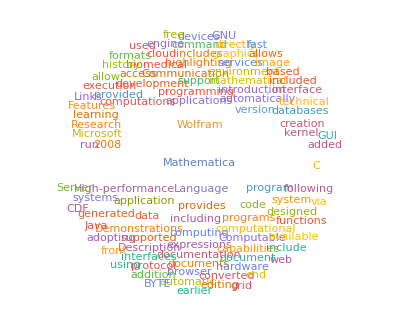

```mathematica
WordCloud[WikipediaData["Mathematica"]]
```

```mathematica
Crash Course in Mathematica for Graduate Students
```

## Introduction Lesson 3

In the previous lessons we learnt a lot about the main functionalities of MATHEMATICA, but there is a lot of more! Here we ar going to see some additional functionalities of MATHEMATICA.

```mathematica
RulePlot[CellularAutomaton[30], {{1}, 0}, 50, Mesh->True, PlotLegends->"Icon", ImageSize->Large]
```

-Graphics-

## Pitfalls and your own function

It could be useful to implement your own function in MATHEMATICA. We have already done it in the ‘Eigenmodes of the Heat Equation’ section with the L2norm function.

```mathematica
L2norm[f1_, f2_, Domain_:{x, 0, 1}]:=Module[{},
Integrate[Conjugate[f2]*f1, Domain]
]
```

The gray background of that cell indicates it is an Initialization Cell. (Crtl + 8).

Define a trivial function using Module. (example: AddTwo, a function that sums two numbers)

It would be useful to look at some pitfalls and others exotic symbol in MATHEMATICA. For more take a look at [3].

```mathematica
Table[i^2, {i, 1, 10}]
Table[  i^2, {i, 1, #}]&@10
```

{1,4,9,16,25,36,49,64,81,100}

{1,4,9,16,25,36,49,64,81,100}

```mathematica
1+2
(#1 + #2)&@@{1, 2}
```

3

3

## Special Functions and the hydrogen atom

Use the SpericalHarmonicY function to make a SpericalPlot3D and visualize some spherical harmonics.

## Fun with Random Numbers

Do you know how Monte Carlo methods work? Monte Carlo are a broad class of computational algorithms that rely on repeated random sampling to obtain numerical results.  
If you are not confident with MCs take a look at this simple but inspiring example: this is how I figured out MCs.

Consider a  square and a quarter of the radius 1 circle built with the origin on one of the corner of the square. Now spread in the plane a lot of points randomly. We have that

(Area of the circle/4) : (Area of the square) = (# points inside) : (# points overall)

Since the area of the square is 1 we have that
(Area of the circle)/4=π/4=(# points inside)/(# points overall)

Find π using the RandomReal function and give a graphical representation of the process.

## Fun with Machine Learning

```mathematica
ExampleData["Geometry3D"]
```

We can do the same we have done for the cylinder but using weird object in the database.

```mathematica
wrench=ExampleData[{"Geometry3D","Wrench"},"Region"]
```

-Graphics3D-

```mathematica
point={-8,-0.168,0};
Show[wrench,Graphics3D[{PointSize[Large],Point[point]}],ViewPoint->{0,-∞,0}]
```

-Graphics3D-

```mathematica
Inertia=MomentOfInertia[wrench,point]
principalaxes=Eigenvectors[Inertia]
inertiaellipsoid=Ellipsoid[point,1000 Inverse[Inertia]]
```

{{229.671,4.12838,36.4835},{4.12838,23219.4,-0.160962},{36.4835,-0.160962,23004.6}}

{{0.000178434,1.,-0.000718987},{0.00160204,0.000718701,0.999998},{0.999999,-0.000179586,-0.00160191}}

Ellipsoid[{-8,-0.168,0},{{4.35517,-0.000774391,-0.00690696},{-0.000774391,0.0430675,1.52947×10^-6},{-0.00690696,1.52947×10^-6,0.0434805}}]

```mathematica
axes=Graphics3D[{Opacity[1],Arrowheads[{-0.04,0.04}],{Specularity[Gray,10],Gray,inertiaellipsoid},MapThread[{RGBColor[#2],Arrow[Tube[{point-4 #,point+4 #},.06]]}&,{principalaxes,IdentityMatrix[3]}]}];
Show[wrench,axes,BaseStyle->Opacity[0.3]]
```

-Graphics3D-

Also countries data are available.

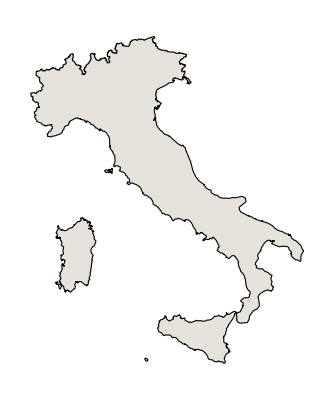

```mathematica
CountryData["Italy", "Shape"]
```

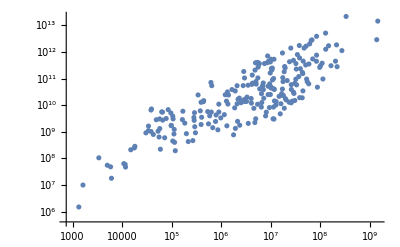

```mathematica
ListLogLogPlot[
 Tooltip[{CountryData[#, "Population"], CountryData[#, "GDP"]}, 
    CountryData[#, "Name"]] & /@ CountryData["Countries"]]
```

Oss.: Also the WordCloud I used as head image...

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}]
Length[titanic]
```

1309

```mathematica
RandomSample[titanic,5]
Normal[%]
```

{<|class→3rd,age→24,sex→male,survived→False|>,<|class→1st,age→55,sex→female,survived→True|>,<|class→3rd,age→Missing[],sex→male,survived→False|>,<|class→3rd,age→21,sex→female,survived→False|>,<|class→2nd,age→26,sex→male,survived→False|>}

```mathematica
titanic[Count[_Missing],"age"]
```

263

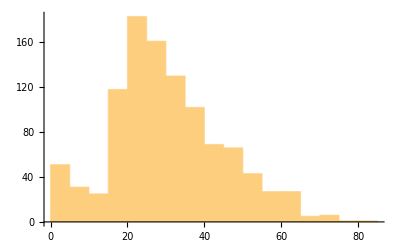

```mathematica
titanic[Histogram,"age"]
```

```mathematica
titanic[Max,"age"]
```

80

```mathematica
ratio[list_]:=list//Boole//Mean//N;
titanic[GroupBy["sex"],GroupBy["class"],ratio,"survived"]
```

## Fun with the Wolfram community

The code here is taken from [5]. In general looking inside the Wolfram Community is always a good idea if you want to find interesting stuff.

```mathematica
ClearAll (*clear variables saves life*)
```

ClearAll

```mathematica
terms=20;
λx[1]=N[Table[n π,{n,1,terms}]];
λy[1]=N[Table[(m π)/A,{m,1,terms}]];
λ2[1]=Table[(λx[1][[m]])^2+(λy[1][[n]])^2,{m,1,terms},{n,1,terms}];
λx[2]=N[Table[n π,{n,0,terms-1}]];
λy[2]=N[Table[(m π)/A,{m,0,terms-1}]];
λ2[2]=Table[(λx[2][[m]])^2+(λy[2][[n]])^2,{m,1,terms},{n,1,terms}];
ψx[1]=Sin[λx[1]*x];
ψy[1]=Sin[λy[1]*y];
ψ[1]=Transpose[{ψx[1]}].{ψy[1]};
ψx[2]=Cos[λx[2]*x];
ψy[2]=Cos[λy[2]*y];
ψ[2]=Transpose[{ψx[2]}].{ψy[2]};
Nx[1]=Table[1/2,{i,1,terms}];
Ny[1]=Table[A/2,{i,1,terms}];
Nx[2]=Prepend[Table[1/2,{i,1,terms-1}],1];
Ny[2]=Prepend[Table[A/2,{i,1,terms-1}],A];
ψxint[1]=1/Nx[1](Integrate[Sin[lam*x],{x,xstart,xend}]/.lam->λx[1]);
ψyint[1]=1/Ny[1](Integrate[Sin[lam*y],{y,ystart,yend}]/.lam->λy[1]);
ψint[1]=Transpose[{ψxint[1]}].{ψyint[1]};
ψxint[2]=1/Nx[2] Prepend[Integrate[Cos[lam*x],{x,xstart,xend}]/.lam->λx[2][[2;;terms]],(xend-xstart)];
ψyint[2]=1/Ny[2] Prepend[Integrate[Cos[lam*y],{y,ystart,yend}]/.lam->λy[2][[2;;terms]],(yend-ystart)];
ψint[2]=Transpose[{ψxint[2]}].{ψyint[2]};
Eint[1]=2*Exp[-B*t/2]*Sin[t/2*√(4*λ2[1]-B^2)]/√(4*λ2[1]-B^2);
Eint[2]=2*Exp[-B*t/2]*Sin[t/2*√(4*λ2[2]-B^2)]/√(4*λ2[2]-B^2);
Solution[1][x_,y_,t_,xstart_,ystart_,xend_,yend_,A_,B_]=Total[Eint[1]*ψint[1]*ψ[1],2];
Solution[2][x_,y_,t_,xstart_,ystart_,xend_,yend_,A_,B_]=Total[Eint[2]*ψint[2]*ψ[2],2];
```

```mathematica
Manipulate[
If[Spts[[2]]>A-.05,Spts={Spts[[1]],A-.05}];
Plot3D[
Evaluate[
Solution[BC][x,y,t,Spts[[1]]-.05,Spts[[2]]-.05,Spts[[1]]+.05,Spts[[2]]+.05,A,B]
],
{x,0,1},{y,0,A},
PlotRange->0.04{-1,1},
BoxRatios->{1,A,5/8},
PlotPoints->ControlActive[30,50],
MaxRecursion->2,
Boxed->False,
Axes->False,
Mesh-> False,
SphericalRegion-> True],
{{t,0,"time"},0,2*√2,0.01,Appearance->"Labeled"},
{{A,1,"aspect ratio"},.1,1,Appearance->"Labeled"},
{{B,0.001,"damping"},0.001,2,Appearance->"Labeled"},
{{BC,1,"boundaries"},{1->" fixed ",2->" free "}},
{{Spts,{.5,.5},"source point "},{.05,.05},{.95,A-.05},ControlType->Slider2D},

ControlPlacement->{Top,Top,Top,Left,Left},
SaveDefinitions->True,
AutorunSequencing-> {1},
SynchronousInitialization-> False,
SynchronousUpdating-> False]
```

## Fun with the Wolfram Model

Double slit experiment using the Wolfram Model.

## Your first Mathematica package

Write a Mathematica package for numerical evaluation of one-dimensional integral using the same MC technique we used to determine π. Load the package with the Get (or Needs) function and play with it.

## Different Loops Comparison

We extensively used the Table function. On the other hand, in C++/Python languages we are used to make loops with For and While functions. Here we make a comparison between Table and other loop functions to explain why it’s always a good idea to prefer Table if possible.

```mathematica
for=Table[Module[{i},For[i=1,i≤10^n,i++,i^2]//AbsoluteTiming//First],{n,1,7}]; (*for 'for' and 'while' loops there is also the Module subtlety*)
while=Table[Module[{i},i=1;While[i≤10^n,i^2;i++]//AbsoluteTiming//First],{n,1,7}];
do=Table[Do[i^2,{i,10^n}]//AbsoluteTiming//First,{n,1,7}];
table=Table[Table[i^2,{i,10^n}];//AbsoluteTiming//First,{n,1,7}];
range=Table[Range[10^n]^2;//AbsoluteTiming//First,{n,1,7}];
```

```mathematica
Last/@{for,while,do,table,range}
```

{7.87839,8.81159,2.56355,0.20672,0.021239}

```mathematica
ListLogPlot[{for,while,do,table,range},Frame->True,PlotRange->All,Joined->True,ImageSize->Large,FrameLabel->{"n","Log[AbsoluteTiming] (sec)"},PlotLabels->{"For","While","Do","Table","Range"}]
```

-Graphics-

## Python with External Evaluators and MathLink

```mathematica
RegisterExternalEvaluator["Python", "/usr/bin/python3"]
FindExternalEvaluators["Python"]
```

ed5ce3c6-a48f-6dbb-1139-8a8f5e06b7e8

Open Python cell => Shift  +  >

Try to write a trivial script in Python and check if it works.

It is also possible to link MATHEMATICA with other external programs. AN idea is to use Mathlink, for more see [].

## Wolfram scripts

Curiosity: it is possible also to write scripts using the Wolfram Language (called wolframscript) similarly to Python. (show test wls script)

Try to write and run (from the terminal) a trivial script using the Wolfram Language.

## References

[1] A Mathematica Primer for Physicists, Jim Napolitano
[2] https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
[3] https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616
[4] https://reference.wolfram.com/language/tutorial/Lists.html#2534
[5] https://demonstrations.wolfram.com/2DWavePropagation/
[6] https://mathematica.stackexchange.com/questions/134609/why-should-i-avoid-the-for-loop-in-mathematica
[7] https://reference.wolfram.com/language/ref/Module.html